```mathematica
f[k_] =1/2 1/(4 Pi k) (1 - Exp[- 2 Pi k] );
```

### Martingale data : N = 512, interval size = 512, 512 samples k = 3

```mathematica
M3 = {0.0389304+I*(-0.00894224),0.0204769+I*(0.0496989),0.0665087+I*(0.0729081),-0.0622991+I*(0.0613657),-0.0246592+I*(0.0800287),-0.0574989+I*(0.0492246),-0.0843104+I*(0.0951129),-0.0173243+I*(0.127711),0.0100645+I*(0.0417716),0.025882+I*(0.0750044),0.0221562+I*(0.121474),-0.084103+I*(0.164607),-0.0781461+I*(0.1488),-0.00184712+I*(0.148237),-0.0437886+I*(0.195494),-0.131098+I*(0.188155),-0.12417+I*(0.191988),-0.090534+I*(0.215451),-0.112611+I*(0.161172),-0.105962+I*(0.151682),-0.0994313+I*(0.157563),-0.120269+I*(0.199137),-0.0791004+I*(0.212027),0.00259583+I*(0.160008),-0.0546747+I*(0.10691),-0.0003413+I*(0.082628),0.0311447+I*(0.0617381),0.00104168+I*(0.0670957),0.00325947+I*(0.00809059),-0.0319017+I*(-0.0152728),-0.159481+I*(-0.0212139),-0.14555+I*(-0.00626577),-0.0851408+I*(-0.00772616),-0.0726886+I*(-0.0160714),0.0655332+I*(-0.0229948),0.0765819+I*(0.000114168),0.0275312+I*(0.00237239),0.0313326+I*(0.0130861),0.0240036+I*(0.00375598),0.00656199+I*(0.0258285),-0.00433628+I*(0.0365924),0.00952039+I*(0.0345132),-0.0279358+I*(0.0244527),-0.00304884+I*(-0.00574767),0.0128975+I*(-0.0801212),0.0704464+I*(-0.0239684),0.108692+I*(-0.0401188),0.0756854+I*(0.00820778),0.12696+I*(0.0623378),0.0750145+I*(0.0996121),0.0858978+I*(0.0640823),0.147415+I*(0.027434),0.128013+I*(0.024686),0.171695+I*(0.014601),0.138351+I*(-0.0602952),0.207197+I*(-0.0318389),0.203343+I*(-0.0398348),0.153255+I*(-0.0139466),0.160746+I*(0.0391351),0.1339+I*(0.0311325),0.138099+I*(0.0541614),0.196505+I*(0.0908393),0.132007+I*(0.0369856),0.00415858+I*(0.0295242),-0.0121409+I*(-0.00661676),0.00705144+I*(-0.0176101),0.021655+I*(-0.00773828),-0.0677813+I*(0.0416197),-0.00830954+I*(0.0340879),-0.0422954+I*(0.031477),-0.0343087+I*(0.00595364),0.000312798+I*(-0.0702967),0.0684717+I*(-0.106537),0.0734543+I*(-0.206403),0.105962+I*(-0.12003),0.0938183+I*(-0.0855632),0.158811+I*(-0.132001),0.179576+I*(-0.132955),0.117631+I*(-0.164424),0.120641+I*(-0.164881),0.0539335+I*(-0.112734),0.0702398+I*(-0.139359),0.0864979+I*(-0.135933),0.0511737+I*(-0.0403886),0.0523922+I*(0.0126609),0.0516514+I*(0.0349784),0.0339932+I*(0.00952123),0.0490954+I*(0.0665994),0.0357626+I*(0.101947),0.0310291+I*(0.124472),0.0128485+I*(0.195392),-0.0447076+I*(0.239463),-0.0737342+I*(0.319798),-0.113119+I*(0.237134),-0.156837+I*(0.179311),-0.160357+I*(0.163663),-0.18673+I*(0.137244),-0.195216+I*(0.0749909),-0.117326+I*(0.0608403),-0.0526128+I*(0.0354252),-0.0577381+I*(0.0785363),-0.124076+I*(0.103625),-0.133826+I*(0.0885461),-0.117223+I*(0.0900683),-0.159392+I*(0.111079),-0.167955+I*(0.124975),-0.0694426+I*(0.00162436),-0.0386431+I*(0.0252501),-0.0858142+I*(-0.0268184),-0.113073+I*(-0.0575176),-0.0570029+I*(0.0112103),-0.0151649+I*(0.0253333),-0.0710372+I*(0.0219155),-0.0620017+I*(-0.0300868),-0.0726779+I*(-0.0296648),-0.100551+I*(-0.0369923),-0.0691019+I*(-0.0435251),-0.103062+I*(-0.020122),-0.0676975+I*(-0.0944994),-0.00417308+I*(0.0173247),-0.0433505+I*(0.0158466),-0.0457961+I*(0.0909723),-0.0755471+I*(0.099178),-0.0982708+I*(0.0337268),-0.0827079+I*(0.0235431),-0.0687307+I*(-0.023147),-0.159325+I*(-0.0963088),-0.145828+I*(-0.170161),-0.165066+I*(-0.121935),-0.137855+I*(-0.0799895),-0.140837+I*(-0.03262),0.00586629+I*(-0.0836394),-0.0262914+I*(-0.096645),-0.0397494+I*(-0.0785427),-0.0655255+I*(-0.0588186),-0.101058+I*(-0.131408),-0.103648+I*(-0.111014),-0.125936+I*(-0.072747),-0.117579+I*(-0.0641812),-0.0511248+I*(-0.0167388),0.0371303+I*(0.0253983),0.0452917+I*(-0.0234158),-0.0187001+I*(0.0101684),-0.0765188+I*(0.0161722),-0.0910448+I*(0.0329915),-0.0779055+I*(0.132048),-0.0409607+I*(0.0909527),-0.0489933+I*(0.0855291),-0.0424634+I*(0.0637031),0.0251361+I*(0.0877899),0.0620058+I*(0.0575628),0.0527826+I*(0.101875),0.0883221+I*(0.0696596),0.202764+I*(0.14087),0.196834+I*(0.087256),0.161548+I*(0.133064),0.16168+I*(0.0680114),0.140717+I*(-0.00774548),0.103635+I*(-0.020935),0.154801+I*(-0.0532051),0.108195+I*(-0.0432773),0.0585909+I*(0.0271654),0.0769919+I*(-0.0507707),0.0884287+I*(-0.095538),0.130362+I*(-0.11667),0.113572+I*(-0.114693),0.194586+I*(-0.0425141),0.113594+I*(-0.0867584),0.15347+I*(-0.0548833),0.122198+I*(-0.0714377),0.0927491+I*(-0.0068291),0.0940461+I*(0.000156747),0.0981064+I*(0.0264465),0.066066+I*(-0.0367532),0.0973259+I*(0.00192201),0.159889+I*(0.0183541),0.179464+I*(0.0175966),0.234831+I*(0.0203309),0.233845+I*(0.0240589),0.266141+I*(0.0570988),0.220268+I*(0.0269229),0.242517+I*(-0.0210156),0.255768+I*(-0.0723343),0.235897+I*(-0.0795245),0.130117+I*(-0.0871958),0.0812257+I*(-0.10148),0.104239+I*(-0.13766),0.109817+I*(-0.131286),0.133494+I*(-0.17182),0.114993+I*(-0.166678),0.0704227+I*(-0.127407),0.090713+I*(-0.109724),0.164486+I*(-0.0927066),0.237591+I*(-0.0974088),0.262841+I*(-0.0199001),0.353471+I*(-0.0816155),0.381461+I*(-0.101963),0.380378+I*(-0.0476106),0.374525+I*(-0.0554383),0.421518+I*(0.0147341),0.436413+I*(0.00920928),0.333451+I*(0.0403196),0.30081+I*(0.0501458),0.282852+I*(0.0913719),0.336318+I*(0.0871926),0.315683+I*(0.0795337),0.272997+I*(0.0630296),0.216304+I*(0.0892113),0.183855+I*(0.0784921),0.178285+I*(0.121532),0.151786+I*(0.154014),0.163891+I*(0.157987),0.211491+I*(0.168355),0.243634+I*(0.169102),0.167014+I*(0.0950375),0.23051+I*(0.0634507),0.214917+I*(0.0947925),0.175036+I*(0.060075),0.109858+I*(0.0254566),0.0590343+I*(-0.0178298),0.00661061+I*(-0.0469928),-0.0120129+I*(-0.0867253),0.025533+I*(-0.141956),-0.00405592+I*(-0.189264),0.0190434+I*(-0.153407),0.0253901+I*(-0.160901),0.0573287+I*(-0.114425),0.0145478+I*(-0.0672851),0.0467213+I*(-0.0901043),0.0114839+I*(-0.0983533),0.000211037+I*(-0.146405),-0.00167622+I*(-0.112387),-0.0878881+I*(-0.165333),-0.0423617+I*(-0.155757),-0.0611394+I*(-0.168992),-0.0786547+I*(-0.170655),-0.0908178+I*(-0.20368),-0.157213+I*(-0.153027),-0.113994+I*(-0.086132),-0.114444+I*(-0.0824549),-0.0226881+I*(-0.0648047),-0.0300036+I*(-0.0681693),-0.0770322+I*(-0.00790276),-0.0998599+I*(-0.0088596),-0.0986947+I*(-0.0478006),-0.138984+I*(-0.0706466),-0.104845+I*(-0.116681),-0.149173+I*(-0.100225),-0.175507+I*(-0.0976677),-0.139885+I*(-0.100515),-0.140729+I*(-0.0438533),-0.137295+I*(-0.103374),-0.109262+I*(-0.156807),-0.119817+I*(-0.256783),-0.102578+I*(-0.290446),-0.0919509+I*(-0.260078),-0.0923712+I*(-0.171879),-0.0333842+I*(-0.113826),0.0106813+I*(-0.154385),0.0370577+I*(-0.113839),0.100028+I*(-0.0463131),0.14832+I*(-0.0354307),0.135996+I*(0.0621563),0.0626619+I*(0.00433499),0.10749+I*(0.027757),0.0995355+I*(0.0328822),0.0539593+I*(0.0112309),0.104296+I*(0.0200038),0.036883+I*(-0.0345905),0.0299141+I*(-0.0185828),0.0276401+I*(-0.0355096),-0.00872779+I*(-0.0300595),0.0117744+I*(-0.0559091),0.0550676+I*(-0.0965678),-0.024596+I*(-0.134142),-0.0810357+I*(-0.0540741),-0.0137815+I*(-0.0862785),0.0363605+I*(-0.102491),0.0255754+I*(-0.0884285),-0.024994+I*(-0.0529624),-0.0221449+I*(0.0225754),0.0450823+I*(0.0870495),0.0253127+I*(0.107176),0.0542347+I*(0.0998233),0.0873763+I*(0.0393196),0.0347739+I*(0.0464162),0.0575184+I*(-0.0105413),0.055255+I*(0.0801088),0.108683+I*(0.0862904),0.0927382+I*(0.0824547),0.121299+I*(0.03661),0.137054+I*(0.0740056),0.111858+I*(0.0954604),0.124621+I*(0.144447),0.0589067+I*(0.119829),0.0153223+I*(0.187688),-0.0444252+I*(0.232669),-0.0872271+I*(0.168011),-0.101359+I*(0.147771),-0.0592014+I*(0.0322116),-0.0969955+I*(0.0359488),-0.0546027+I*(0.0295019),-0.11886+I*(-0.0473933),-0.16525+I*(0.0971239),-0.147642+I*(0.158396),-0.150658+I*(0.164702),-0.171618+I*(0.188065),-0.159278+I*(0.157122),-0.167899+I*(0.200606),-0.117099+I*(0.199358),0.00336189+I*(0.231875),0.0308791+I*(0.195807),-0.0166764+I*(0.220321),-0.0435433+I*(0.153373),-0.0930483+I*(0.0971371),-0.042416+I*(0.075666),-0.052088+I*(-0.0228768),0.0530853+I*(0.0291132),0.076801+I*(0.0949284),0.0628142+I*(0.0529235),0.0246207+I*(-0.00590707),-0.0524586+I*(-0.0257279),-0.00182633+I*(-0.0614934),-0.040544+I*(-0.052691),-0.0141239+I*(-0.0497587),0.0207118+I*(-0.00322778),0.0237207+I*(0.052153),0.050212+I*(0.101204),0.00795822+I*(0.0616207),0.0200206+I*(0.0384632),0.0436863+I*(0.0811615),0.0416978+I*(0.0435505),-0.000235447+I*(0.0654745),-0.0146101+I*(0.0727884),-0.00954258+I*(0.0686478),0.0169605+I*(0.0482531),0.0579556+I*(0.0581192),0.12455+I*(0.115489),0.0583286+I*(0.122832),0.0413691+I*(0.0941306),0.0594518+I*(0.0710209),0.0685967+I*(0.0228341),0.0498443+I*(-0.0309762),0.0912455+I*(-0.0300694),0.0588645+I*(-0.0421645),0.12634+I*(-0.0763756),0.136898+I*(0.0247702),0.157661+I*(0.00192757),0.153205+I*(-0.00529516),0.177221+I*(0.0223076),0.211743+I*(-0.0427768),0.148239+I*(-0.0160353),0.125735+I*(-0.0243161),0.166853+I*(-0.00618172),0.0648305+I*(0.0537178),0.0403944+I*(0.0579133),0.0851628+I*(0.044394),0.0257936+I*(-0.019064),-0.0469026+I*(-0.0179274),-0.0830889+I*(0.0339486),-0.0434643+I*(0.0810477),0.00777218+I*(0.0637604),0.0625509+I*(0.0717996),0.162889+I*(0.0777317),0.0801269+I*(0.109991),0.156875+I*(0.049525),0.172407+I*(0.00979103),0.267305+I*(0.0716374),0.347675+I*(0.153864),0.36594+I*(0.152805),0.299468+I*(0.132085),0.291687+I*(0.192043),0.280168+I*(0.172895),0.199256+I*(0.139356),0.160162+I*(0.0555466),0.167996+I*(0.0903621),0.183843+I*(0.0251754),0.197038+I*(0.0547719),0.179541+I*(0.0553964),0.18195+I*(0.0641301),0.164751+I*(0.110128),0.109928+I*(0.152566),0.0958727+I*(0.135442),0.113861+I*(0.0952326),0.142185+I*(-0.0170067),0.0837653+I*(-0.0109686),0.145234+I*(-0.100498),0.118045+I*(-0.101835),0.0672865+I*(-0.132761),0.0594126+I*(-0.0970897),0.0690192+I*(-0.0767095),0.0508504+I*(-0.116139),0.044337+I*(-0.0860827),0.0563194+I*(-0.0794015),0.0461711+I*(-0.0703602),-0.0493867+I*(-0.0931622),-0.0438098+I*(-0.0575279),-0.0129037+I*(-0.0581538),-0.039592+I*(-0.137751),-0.131771+I*(-0.115663),-0.0464205+I*(-0.144435),0.0541223+I*(-0.169939),0.0352774+I*(-0.168673),-0.0192489+I*(-0.0731734),-0.0374622+I*(-0.0407794),-0.0190431+I*(-0.0377432),-0.0909976+I*(-0.0220919),-0.129079+I*(0.00831207),-0.172627+I*(-0.0117749),-0.16969+I*(-0.0158858),-0.149379+I*(-0.0821255),-0.146411+I*(-0.0867601),-0.1443+I*(-0.106238),-0.0992053+I*(-0.110461),-0.127867+I*(-0.0977335),-0.105069+I*(-0.106803),-0.118073+I*(-0.108019),-0.0668114+I*(-0.114188),-0.164173+I*(-0.0478215),-0.123964+I*(-0.0425209),-0.174919+I*(0.0326781),-0.25916+I*(0.0590748),-0.302883+I*(0.0183452),-0.240548+I*(0.0347877),-0.212422+I*(-0.019399),-0.204401+I*(0.0167476),-0.208587+I*(-0.000462469),-0.242096+I*(0.0122857),-0.181715+I*(-0.0862269),-0.263836+I*(-0.0171759),-0.249688+I*(0.0579956),-0.205273+I*(0.0576123),-0.204125+I*(0.071003),-0.187537+I*(0.118354),-0.21683+I*(0.143587),-0.242157+I*(0.102978),-0.221957+I*(0.0838973),-0.199325+I*(0.10999),-0.174482+I*(0.078799),-0.203649+I*(0.0751174),-0.241459+I*(0.0454701),-0.233894+I*(0.0163297),-0.268472+I*(0.0160648),-0.295625+I*(-0.0303583),-0.242162+I*(-0.034909),-0.195261+I*(-0.0355452),-0.152617+I*(-0.0134733),-0.153646+I*(0.0331332),-0.177417+I*(0.00712798),-0.124456+I*(-0.0350923),-0.0229435+I*(-0.0769998),-0.0383426+I*(-0.0157679),-0.0653929+I*(0.00587766),-0.00998866+I*(-0.0125336),-0.0361639+I*(0.0443154),-0.0377291+I*(0.0619079),0.0466101+I*(0.0282038),0.0201131+I*(0.0183695),-0.0742604+I*(0.0222895),-0.132817+I*(-0.0327642),-0.187656+I*(-0.026108),-0.207542+I*(-0.0433052),-0.234331+I*(-0.0155261),-0.25343+I*(-0.0501173),-0.250648+I*(0.0423473),-0.204727+I*(0.0157516),-0.209081+I*(0.00932114),-0.217195+I*(0.0381501),-0.147657+I*(0.00271499),-0.148983+I*(0.0241169),-0.148075+I*(0.0197816),-0.12628+I*(0.0401457),-0.136878+I*(0.0970011),-0.178302+I*(0.0624396),-0.194156+I*(0.0399581),-0.250987+I*(0.0249275),-0.259616+I*(0.0086313),-0.289295+I*(0.0592255),-0.26729+I*(0.108396),-0.243998+I*(0.174929),-0.188404+I*(0.218871),-0.181017+I*(0.112254),-0.143159+I*(0.071331),-0.146567+I*(0.0904393),-0.18941+I*(0.113535),-0.135826+I*(0.137102),-0.0469641+I*(0.113909),-0.0353083+I*(0.0916471),0.00602522+I*(0.131104),0.00529348+I*(0.12905),-0.0457732+I*(0.134484),-0.117841+I*(0.15228),-0.204202+I*(0.138644),-0.216524+I*(0.179576),-0.233369+I*(0.140227),-0.250798+I*(0.121027),-0.211165+I*(0.162545),-0.13866+I*(0.173958),-0.123091+I*(0.183439),-0.131807+I*(0.180787),-0.119508+I*(0.201025),-0.182758+I*(0.232787),-0.112785+I*(0.230279),-0.130803+I*(0.192314),-0.13553+I*(0.128504),-0.116016+I*(0.141847),-0.0611557+I*(0.0927679),-0.102792+I*(0.0586119),-0.158324+I*(-0.0470562),-0.102951+I*(-0.114301),-0.132839+I*(-0.122551),-0.117081+I*(-0.144295)};
```

### Analysis

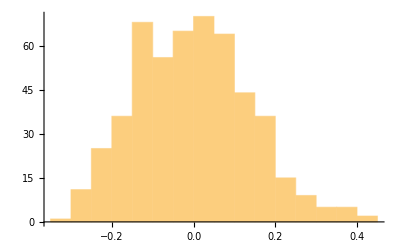

```mathematica
Histogram[Re[M3]]
```

```mathematica
d3 = HistogramDistribution[Re[M3]];
```

```mathematica
Moment[d3, 1]
Moment[d3, 2]
f[3.]
```

-0.00205078

0.0196419

0.0132629

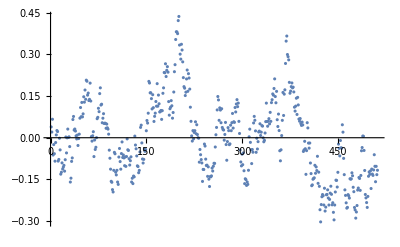

```mathematica
ListPlot[Re[M3]]
```